```mathematica
SetDirectory["~/src/MathematicaScripts/Josh_FCS"]
```

/Users/joshtitlow/src/MathematicaScripts/Josh_Fcs

```mathematica
FileNames[]
```

{1B_1sp2D.xlsx,1B_2sp2D.xlsx,1B_2sp3D.xlsx,._RSS_calc.xlsx,RSS_calc.xlsx,~$1B_2sp3D.xlsx,~$RSS_calc.xlsx}

```mathematica
data=Import["1B_1sp2D.xlsx"]
data1=Import["1B_2sp2D.xlsx"]
data2=Import["1B_2sp3D.xlsx"]
data3=Import["Gs_1sp2D.xlsx"]
data4=Import["Gs_1sp3D.xlsx"]
data5=Import["Gs_2sp2D.xlsx"]
```

{{{,Time (ms),20160506_Orb2GFP_0xK_p1s3r_branch1_1_CH0,20160506_Orb2GFP_0xK_p1s3r_branch1_1_CH0 fitted model: ,20160506_Orb2GFP_0xK_p1s3r_branch1_2_CH0,20160506_Orb2GFP_0xK_p1s3r_branch1_2_CH0 fitted model: ,20160506_Orb2GFP_0xK_p1s3r_branch1_3_CH0,20160506_Orb2GFP_0xK_p1s3r_branch1_3_CH0 fitted model: ,20160506_Orb2GFP_0xK_p1s3r_branch1_4_CH0,303,RSS201,RSS203,RSS205,RSS207,RSS209,,,,},131,{,,317,,}}}
 |  |  |  |

{{{,Time (ms),20160506_Orb2GFP_0xK_p1s3r_branch1_1_CH0,20160506_Orb2GFP_0xK_p1s3r_branch1_1_CH0 fitted model: ,20160506_Orb2GFP_0xK_p1s3r_branch1_2_CH0,20160506_Orb2GFP_0xK_p1s3r_branch1_2_CH0 fitted model: ,20160506_Orb2GFP_0xK_p1s3r_branch1_3_CH0,309,RSS209,,,,20160506_Orb2GFP_5xK_p3s3l_branch5_3_CH0,20160506_Orb2GFP_5xK_p3s3l_branch5_3_CH0 fitted model: ,20160506_Orb2GFP_5xK_p3s3l_branch5_3_CH0 fitted model: },135,{1}}}
 |  |  |  |

{{{,Time (ms),20160506_Orb2GFP_0xK_p1s3r_branch1_1_CH0,20160506_Orb2GFP_0xK_p1s3r_branch1_1_CH0 fitted model: ,20160506_Orb2GFP_0xK_p1s3r_branch1_2_CH0,202,20160506_Orb2GFP_5xK_p3s3l_branch5_1_CH0 fitted model: ,20160506_Orb2GFP_5xK_p3s3l_branch5_2_CH0,20160506_Orb2GFP_5xK_p3s3l_branch5_2_CH0 fitted model: ,20160506_Orb2GFP_5xK_p3s3l_branch5_3_CH0,20160506_Orb2GFP_5xK_p3s3l_branch5_3_CH0 fitted model: },119,{119.,210,0.9999}}}
 |  |  |  |

{{{,Time (ms),20160506_Orb2GFP_0xK_p1s3r_branch1_1_CH0,20160506_Orb2GFP_0xK_p1s3r_branch1_1_CH0 fitted model: ,20160506_Orb2GFP_0xK_p1s3r_branch1_2_CH0,202,20160506_Orb2GFP_5xK_p3s3l_branch5_1_CH0 fitted model: ,20160506_Orb2GFP_5xK_p3s3l_branch5_2_CH0,20160506_Orb2GFP_5xK_p3s3l_branch5_2_CH0 fitted model: ,20160506_Orb2GFP_5xK_p3s3l_branch5_3_CH0,20160506_Orb2GFP_5xK_p3s3l_branch5_3_CH0 fitted model: },118,{118.,210,0.999563}}}
 |  |  |  |

{{{,Time (ms),20160506_Orb2GFP_0xK_p1s3r_branch1_1_CH0,20160506_Orb2GFP_0xK_p1s3r_branch1_1_CH0 fitted model: ,20160506_Orb2GFP_0xK_p1s3r_branch1_2_CH0,202,20160506_Orb2GFP_5xK_p3s3l_branch5_1_CH0 fitted model: ,20160506_Orb2GFP_5xK_p3s3l_branch5_2_CH0,20160506_Orb2GFP_5xK_p3s3l_branch5_2_CH0 fitted model: ,20160506_Orb2GFP_5xK_p3s3l_branch5_3_CH0,20160506_Orb2GFP_5xK_p3s3l_branch5_3_CH0 fitted model: },118,{118.,210,0.999563}}}
 |  |  |  |

{{{,Time (ms),20160506_Orb2GFP_0xK_p1s3r_branch1_1_CH0,20160506_Orb2GFP_0xK_p1s3r_branch1_1_CH0 fitted model: ,20160506_Orb2GFP_0xK_p1s3r_branch1_2_CH0,202,20160506_Orb2GFP_5xK_p3s3l_branch5_1_CH0 fitted model: ,20160506_Orb2GFP_5xK_p3s3l_branch5_2_CH0,20160506_Orb2GFP_5xK_p3s3l_branch5_2_CH0 fitted model: ,20160506_Orb2GFP_5xK_p3s3l_branch5_3_CH0,20160506_Orb2GFP_5xK_p3s3l_branch5_3_CH0 fitted model: },118,{118.,210,0.999563}}}
 |  |  |  |

```mathematica
data[[1]]
```

{{Time (ms),20160506_Orb2GFP_0xK_p1s3r_branch1_1_CH0,20160506_Orb2GFP_0xK_p1s3r_branch1_1_CH0 fitted model: ,20160506_Orb2GFP_0xK_p1s3r_branch1_2_CH0,20160506_Orb2GFP_0xK_p1s3r_branch1_2_CH0 fitted model: ,20160506_Orb2GFP_0xK_p1s3r_branch1_3_CH0,20160506_Orb2GFP_0xK_p1s3r_branch1_3_CH0 fitted model: ,20160506_Orb2GFP_0xK_p1s3r_branch1_4_CH0,304,RSS203,RSS205,RSS207,RSS209,,,,},131,{,,,314,129.333,,}}
 |  |  |  |

```mathematica
Length[data2[[1]]]
```

121

```mathematica
k=3
```

3

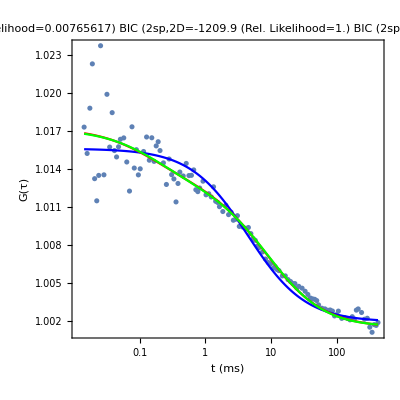
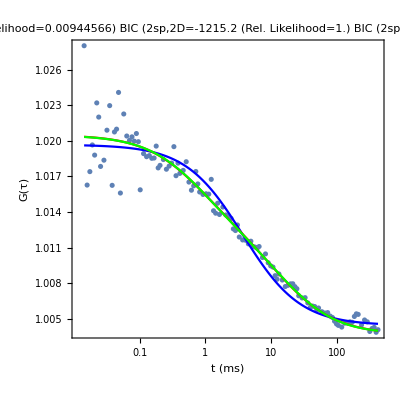
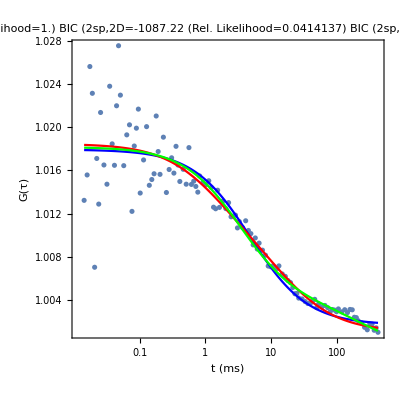
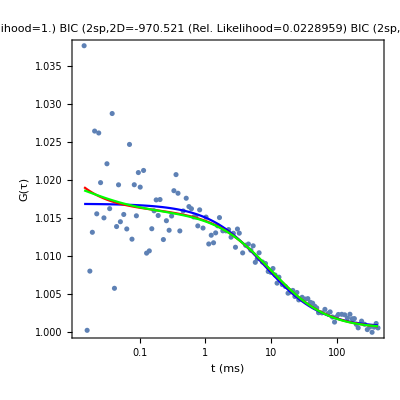
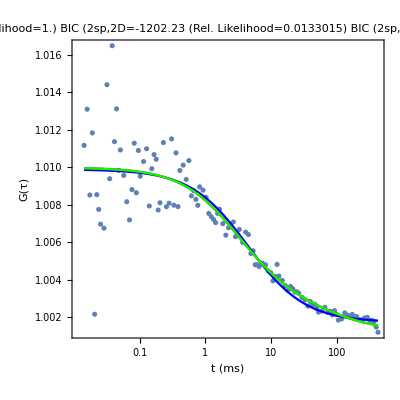
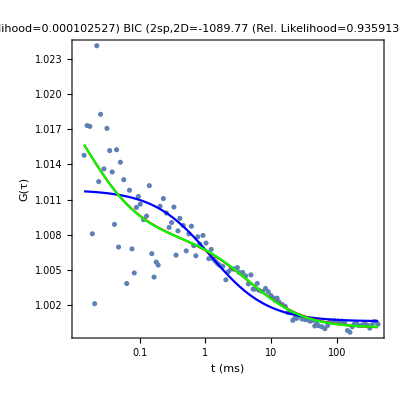
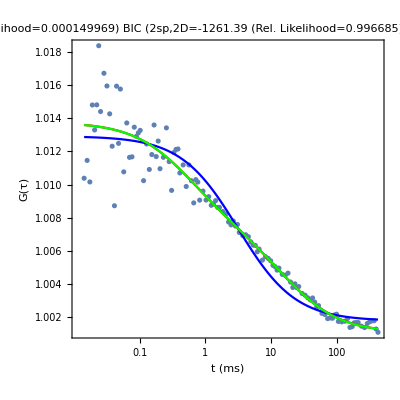
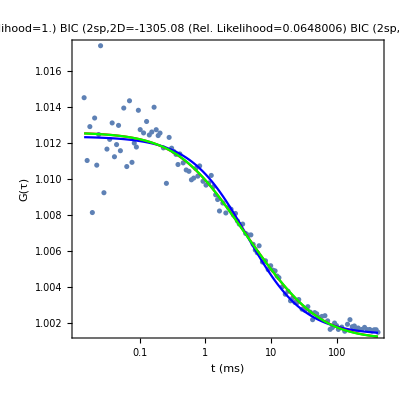

```mathematica
Table[(*RSS*)
RSS[k]=Total[Table[(data[[1]][[j]][[2+k]]-data[[1]][[j]][[2+k+1]])^2,{j,2,120}]];
p1=4;
n=120;
AIC1sp2D[k]=2 (p1+1)+n(Log[2 Pi RSS[k]/n]+1);
BIC1sp2D[k]=Log[n] (p1+1)+n(Log[2 Pi RSS[k]/n]+1);

RSS1[k]=Total[Table[(data1[[1]][[j]][[2+k]]-data1[[1]][[j]][[2+k+1]])^2,{j,2,120}]];
p2=6;
n=120;
AIC2sp2D[k]=2 (p2+1)+n(Log[2 Pi RSS1[k]/n]+1);
BIC2sp2D[k]=Log[n] (p2+1)+n(Log[2 Pi RSS1[k]/n]+1);

RSS2[k]=Total[Table[(data2[[1]][[j]][[2+k]]-data2[[1]][[j]][[2+k+1]])^2,{j,2,120}]];
p3=6;
n=120;
AIC2sp3D[k]=2 (p3+1)+n(Log[2 Pi RSS2[k]/n]+1);
BIC2sp3D[k]=Log[n] (p3+1)+n(Log[2 Pi RSS2[k]/n]+1);

RSS3[k]=Total[Table[(data3[[1]][[j]][[2+k]]-data[[1]][[j]][[2+k+1]])^2,{j,2,120}]];
p4=4;
n=120;
AICGS1sp2D[k]=2 (p1+1)+n(Log[2 Pi RSS3[k]/n]+1);
BICGS1sp2D[k]=Log[n] (p1+1)+n(Log[2 Pi RSS3[k]/n]+1);

RSS4[k]=Total[Table[(data4[[1]][[j]][[2+k]]-data4[[1]][[j]][[2+k+1]])^2,{j,2,120}]];
p5=6;
n=120;
AICGS1sp3D[k]=2 (p2+1)+n(Log[2 Pi RSS4[k]/n]+1);
BICGS1sp3D[k]=Log[n] (p2+1)+n(Log[2 Pi RSS4[k]/n]+1);

RSS5[k]=Total[Table[(data5[[1]][[j]][[2+k]]-data5[[1]][[j]][[2+k+1]])^2,{j,2,120}]];
p6=6;
n=120;
AICGS2sp2D[k]=2 (p3+1)+n(Log[2 Pi RSS5[k]/n]+1);
BICGS2sp2D[k]=Log[n] (p3+1)+n(Log[2 Pi RSS5[k]/n]+1);


dataPlot[k]=Show[ListLogLinearPlot[Table[{data[[1]][[j]][[2]],data[[1]][[j]][[2+k]]},{j,1,121}]],
ListLogLinearPlot[Table[{data[[1]][[j]][[2]],data[[1]][[j]][[2+k+1]]},{j,1,121}],Joined->True,PlotStyle->Blue],ListLogLinearPlot[Table[{data1[[1]][[j]][[2]],data1[[1]][[j]][[2+k+1]]},{j,1,121}],Joined->True,PlotStyle->Red],ListLogLinearPlot[Table[{data2[[1]][[j]][[2]],data2[[1]][[j]][[2+k+1]]},{j,1,121}],Joined->True,PlotStyle->Green],Frame->True,AspectRatio->1,FrameLabel->{"t (ms)","G(τ)"},PlotLabel->StringJoin["BIC (1sp,2D=",ToString[BIC1sp2D[k]]," (Rel. Likelihood=",ToString[likelihood1sp2D[k]=Exp[(Min[BIC1sp2D[k],BIC2sp2D[k],BIC2sp3D[k]]-BIC1sp2D[k])/2]],")","\nBIC (2sp,2D=",ToString[BIC2sp2D[k]]," (Rel. Likelihood=",ToString[likelihood2sp2D[k]=Exp[(Min[BIC1sp2D[k],BIC2sp2D[k],BIC2sp3D[k]]-BIC2sp2D[k])/2]],")","\nBIC (2sp,3D=",ToString[BIC2sp3D[k]]," (Rel. Likelihood=",ToString[likelihood2sp3D[k]=Exp[(Min[BIC1sp2D[k],BIC2sp2D[k],BIC2sp3D[k]]-BIC2sp3D[k])/2]],")",
ToString[likelihood1sp2D[k]=Exp[(Min[BIC1sp2D[k],BIC2sp2D[k],BIC2sp3D[k]]-BIC1sp2D[k])/2]],")",   
 "\nBIC (2sp,2D=",ToString[BIC2sp2D[k]]," (Rel. Likelihood=", 
 ToString[likelihood2sp2D[k]=Exp[(Min[BIC1sp2D[k],BIC2sp2D[k],BIC2sp3D[k]]-BIC2sp2D[k])/2]],")",
 "\nBIC (2sp,3D=",ToString[BIC2sp3D[k]]," (Rel. Likelihood=",
 ToString[likelihood2sp3D[k]=Exp[(Min[BIC1sp2D[k],BIC2sp2D[k],BIC2sp3D[k]]-BIC2sp3D[k])/2]],")"]],{k,1,210,2}]
```

```mathematica
k=1
ListLogLinearPlot[Table[{data[[1]][[j]][[2]],Table[data[[1]][[j]][[2+k]],{k,1,210,2}]},{j,1,121}]]
```

1

-Graphics-

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
loglinearframeticks={{{{Log[0.00001],"0.00001"},{Log[0.00002],""},{Log[0.00003],""},{Log[0.00004],""},{Log[0.00005],""},{Log[0.00006],""},{Log[0.00007],""},{Log[0.00008],""},{Log[0.00009],""},{Log[0.0001],"0.0001"},{Log[0.0002],""},{Log[0.0003],""},{Log[0.0004],""},{Log[0.0005],""},{Log[0.0006],""},{Log[0.0007],""},{Log[0.0008],""},{Log[0.0009],""},{Log[0.001],"0.001"},{Log[0.002],""},{Log[0.003],""},{Log[0.004],""},{Log[0.005],""},{Log[0.006],""},{Log[0.007],""},{Log[0.008],""},{Log[0.009],""},{Log[0.01],"0.01"},{Log[0.02],""},{Log[0.03],""},{Log[0.04],""},{Log[0.05],""},{Log[0.06],""},{Log[0.07],""},{Log[0.08],""},{Log[0.09],""},{Log[0.1],"0.1"},{Log[0.2],""},{Log[0.3],""},{Log[0.4],""},{Log[0.5],""},{Log[0.6],""},{Log[0.7],""},{Log[0.8],""},{Log[0.9],""},{Log[1],"1"},{Log[2],""},{Log[3],""},{Log[4],""},{Log[5],""}},None},{Automatic,None}};
```

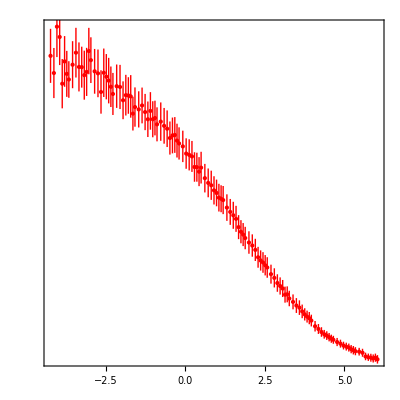

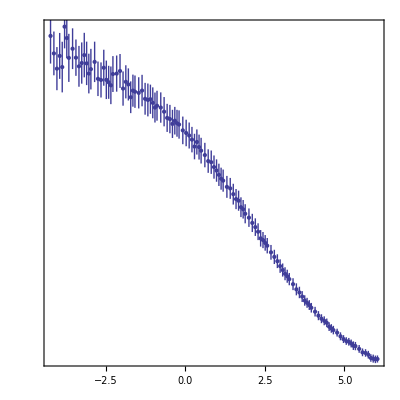

```mathematica
EP1=ErrorListPlot[Table[{{Mean[Table[Log[data[[1]][[j]][[2]]],{k,1,105,2}]],
Mean[Table[data[[1]][[j]][[2+k]],{k,1,105,2}]]},ErrorBar[StandardDeviation[Table[data[[1]][[j]][[2+k]],{k,1,105,2}]]/Sqrt[53]]},{j,2,121}],Frame->True,AspectRatio->1,FrameTicks->loglinearframeticks,PlotStyle->Red]


EP2=ErrorListPlot[Table[{{Mean[Table[Log[data[[1]][[j]][[2]]],{k,107,210,2}]],
Mean[Table[data[[1]][[j]][[2+k]],{k,107,210,2}]]},ErrorBar[StandardDeviation[Table[data[[1]][[j]][[2+k]],{k,107,210,2}]]/Sqrt[53]]},{j,2,121}],Frame->True,AspectRatio->1,FrameTicks->loglinearframeticks]
```

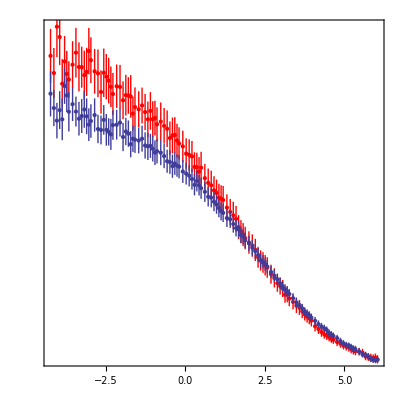

```mathematica
Show[EP1,EP2]
```

```mathematica
Directory[]
```

D:\Josh_Fcs

```mathematica
Export["DataPLot1.tiff",EP1,"TIFF"]
```

DataPLot1.tiff

```mathematica
Table[likelihood1sp2D[k],{k,1,210,2}]
```

{0.00765103,0.00892272,1.,1.,1.,0.000102437,0.000125843,1.,0.316643,0.186752,1.,0.00119698,0.049434,1.,0.0279949,0.00048956,1.,1.14966×10^-6,1.,1.03417×10^-7,0.000597166,1.01891×10^-6,0.182976,0.0016834,0.0265864,0.00218494,0.0000164937,0.00228636,1.,0.114965,0.000297167,0.0170048,0.0493257,0.326326,4.72818×10^-9,0.0000119667,0.00112636,0.000106031,0.141255,1.,0.278188,1.75961×10^-8,8.22077×10^-8,1.,0.143469,0.0000365542,0.631751,0.939247,0.134527,0.000724825,0.0179599,1.,0.039812,1.,0.326058,2.99825×10^-10,3.85573×10^-9,1.04276×10^-7,3.55043×10^-20,1.83632×10^-10,5.04487×10^-8,3.35547×10^-15,4.41596×10^-10,8.91549×10^-7,0.0000156083,2.21903×10^-8,5.4678×10^-8,5.32016×10^-9,1.28582×10^-9,0.137432,0.0129275,0.0175181,0.774556,0.885552,0.0195253,0.0799729,0.0580163,0.302588,1.,1.,1.,2.67896×10^-8,0.000101136,0.00210457,1.,3.42982×10^-9,0.0000141894,0.0275393,1.,1.,1.,1.,0.000748188,1.,0.000115639,1.,1.,0.233318,1.,1.,1.,0.0494925,0.000142828,1.,1.}

```mathematica
BarGraph[Table[likelihood1sp2D[k],{k,1,210,2}]]
```

{0.00765103,0.00892272,1.,1.,1.,0.000102437,0.000125843,1.,0.316643,0.186752,1.,0.00119698,0.049434,1.,0.0279949,0.00048956,1.,1.14966×10^-6,1.,1.03417×10^-7,0.000597166,1.01891×10^-6,0.182976,0.0016834,0.0265864,0.00218494,0.0000164937,0.00228636,1.,0.114965,0.000297167,0.0170048,0.0493257,0.326326,4.72818×10^-9,0.0000119667,0.00112636,0.000106031,0.141255,1.,0.278188,1.75961×10^-8,8.22077×10^-8,1.,0.143469,0.0000365542,0.631751,0.939247,0.134527,0.000724825,0.0179599,1.,0.039812,1.,0.326058,2.99825×10^-10,3.85573×10^-9,1.04276×10^-7,3.55043×10^-20,1.83632×10^-10,5.04487×10^-8,3.35547×10^-15,4.41596×10^-10,8.91549×10^-7,0.0000156083,2.21903×10^-8,5.4678×10^-8,5.32016×10^-9,1.28582×10^-9,0.137432,0.0129275,0.0175181,0.774556,0.885552,0.0195253,0.0799729,0.0580163,0.302588,1.,1.,1.,2.67896×10^-8,0.000101136,0.00210457,1.,3.42982×10^-9,0.0000141894,0.0275393,1.,1.,1.,1.,0.000748188,1.,0.000115639,1.,1.,0.233318,1.,1.,1.,0.0494925,0.000142828,1.,1.}

```mathematica
Mean[Table[likelihood1sp2D[k],{k,1,210,2}]]
Mean[Table[likelihood2sp2D[k],{k,1,210,2}]]
Mean[Table[likelihood2sp3D[k],{k,1,210,2}]]
```

0.338853

0.758277

0.724497

```mathematica
Exp[(Min[BIC[k],BIC1[k]]-BIC[k])/2]
Exp[(Min[BIC[k],BIC1[k]]-BIC1[k])/2]
```

0.000074356

1.

```mathematica
StringJoin["BIC (1sp,2D=",ToString[BIC[k]],"\nBIC (2sp,2D=",ToString[BIC1[k]]]
```

BIC (1sp,2D=-1205.76
BIC (2sp,2D=-1205.76

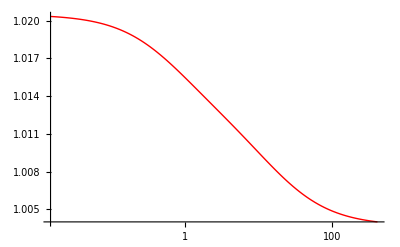

```mathematica
ListLogLinearPlot[Table[{data1[[1]][[j]][[2]],data1[[1]][[j]][[2+k+1]]},{j,1,121}],Joined->True,PlotStyle->Red]
```

```mathematica
Mean[Table[BIC[k],{k,1,105,2}]]
```

-1136.24

```mathematica
Log[10,100]
Log[100]//N
```

2

4.60517